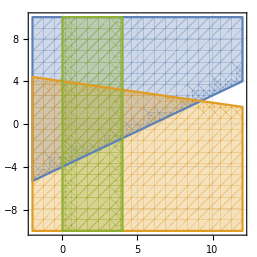

```mathematica
(* https://reference.wolfram.com/language/ref/RegionPlot.html *)
Clear[x];
Clear[y];
f1[x_, y_]:=2x-3y≤12;
f2[x_, y_]:=x+5y≤20;
f3[x_, y_]:=x>0 && x < 4;

RegionPlot[{f1[x, y], f2[x, y],f3[x, y]}, {x,-2, 12},{y,-10, 10},
 GridLines->Automatic]
```

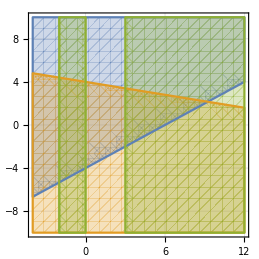

```mathematica
Clear[x];
Clear[y];
f1[x_, y_]:=2x-3y≤12;
f2[x_, y_]:=x+5y≤20;
f3[x_, y_]:=x>3 || (x < 0 && x > -2);

RegionPlot[{f1[x, y], f2[x, y],f3[x, y]}, {x,-4, 12},{y,-10, 10},
 GridLines->Automatic]
```

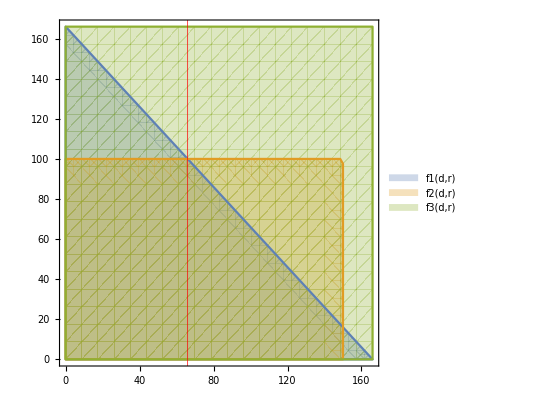

66

```mathematica
(* Airline revenue example, unit 8, edX The Analytics Edge, 2015 *)
Clear[r]; (* Regular seats *)
Clear[d]; (* Discount seats *)
totalCapacity=166; discountDemand = 150; regularDemand = 100;
discountToSell =  totalCapacity - regularDemand;
f1[d_, r_]:=d + r≤ totalCapacity; (* Total seat capacity *)
f2[d_, r_]:=d ≤ discountDemand&& r ≤ regularDemand; (* Demand for Discount and Regular seats *)
f3[d_, r_]:=d≥0 && r ≥ 0; (* Can not sell negative number of seats *)

RegionPlot[{f1[d, r], f2[d, r],f3[d, r]}, {d,0, totalCapacity},{r,0, totalCapacity},GridLines->{{discountToSell}, None}, GridLinesStyle->Red, PlotLegends->"Expressions",
BoundaryStyle-> Automatic]
discountToSell
```

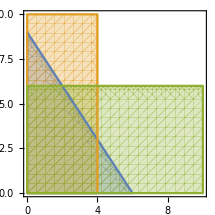

```mathematica
(* Intro to Operations Research, p.28 *)
RegionPlot[{3x+2y<=18, x<=4, 2y<=12}, {x, 0, 10}, {y, 0, 10}]
```

```mathematica
Clear[r, d, discountDemand, regularDemand, totalCapacity];
Func1[d_, r_, capacity_] :=
Module[{},
d + r≤ capacity 
];
Func2[d_, r_, discountDemand_, regularDemand_] :=
Module[{},
d ≤ discountDemand&& r ≤ regularDemand 
];
Func3[d_, r_] :=
Module[{},
d≥0 && r ≥ 0 
];
```

```mathematica
Manipulate[
g = Show[RegionPlot[{Func1[d, r, totalCapacity], Func2[d, r, discountDemand, regularDemand],Func3[d, r]}, {d,0, 200},{r,0, 200},GridLines->{{totalCapacity - regularDemand}, None}, GridLinesStyle->Red, PlotLegends->None,
BoundaryStyle-> Automatic]];

regularPrice =617;
discountPrice = 238;
totalRevenue = (regularDemand * regularPrice) + (discountDemand * discountPrice);
totalRevenueStr = StringForm["Total revenue is: ``",totalRevenue];

Grid[{{g},{totalRevenueStr}}, ItemSize->{{20, 45}}, Frame->None],
 {{totalCapacity, 166, "Total seat capacity"}, 100, 166,1, Appearance->"Labeled"},
 {{discountDemand, 10, "Discount demand"}, 0, 150, 1, Appearance->"Labeled"},
{{regularDemand, 10, "Regular demand"}, 0, totalCapacity, 1, Appearance->"Labeled"},
 SaveDefinitions->True, ControlPlacement->Top]
```